```mathematica
ClearAll[Evaluate[Context[]<>"*"]];
ClearSystemCache[];
```

```mathematica
μ1=Import[NotebookDirectory[]<>"points_f2mu2.m"]//Interpolation;
μ1gauss=Interpolation[Import[NotebookDirectory[]<>"brute_force_points_f2mu2.m"]];
μ1gausspoints=Import[NotebookDirectory[]<>"brute_force_points_f2mu2.m"];
```

```mathematica
μ3=Import[NotebookDirectory[]<>"points_f2mu4.m"]//Interpolation;
μ3gauss=Interpolation[Import[NotebookDirectory[]<>"brute_force_points_f2mu4.m"]];
μ3gausspoints=Import[NotebookDirectory[]<>"brute_force_points_f2mu4.m"];
```

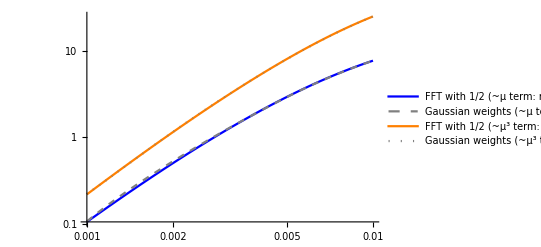

```mathematica
plot=LogLogPlot[{Re[μ1[k]/2],Re[μ1gauss[k]],Re[μ3[k]/2]//Abs,Re[μ3gauss[k]]//Abs},{k,0.001,0.01},PlotLegends->{"FFT with 1/2 (~μ term: recall FFT coefficients do not have 1/2)","Gaussian weights (~μ term)","FFT with 1/2 (~μ^3 term: recall FFT coefficients do not have 1/2)","Gaussian weights (~μ^3 term)"},PlotStyle->{Directive[Blue],Directive[Gray,Dashed],Directive[Orange],Directive[Gray,Dotted]}]
```

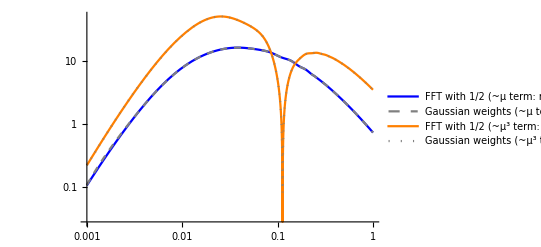

```mathematica
plot=LogLogPlot[{Re[μ1[k]/2],Re[μ1gauss[k]],Re[μ3[k]/2]//Abs,Re[μ3gauss[k]]//Abs},{k,0.001,1},PlotLegends->{"FFT with 1/2 (~μ term: recall FFT coefficients do not have 1/2)","Gaussian weights (~μ term)","FFT with 1/2 (~μ^3 term: recall FFT coefficients do not have 1/2)","Gaussian weights (~μ^3 term)"},PlotStyle->{Directive[Blue],Directive[Gray,Dashed],Directive[Orange],Directive[Gray,Dotted]}]
```

```mathematica
Export[NotebookDirectory[]<>"comparison_plot_final_terms.pdf",plot];
```